For  the unCoVer project - Colombia was used  the  databases published daily by the INS-Colombia. This database includes  the national detected cases infected with SARS-CoV-2 since the start of the pandemic in march 2020 until today. You could contact me to lina.ruiz2@udea.edu.co if you want a complete file with all the downloaded databases used here.  In this notebook is made the processing for the total amount of cases even when they do not get hospitalized (i.e., not admitted to hospital or ICU). The next is an schematic draw of the processing:

### Exploring the matrices

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"];
```

```mathematica
matrix1=Import["dataStructue_15_200.m"];
matrix2=Import["dataStructue_201_210.m"];
matrix3=Import["dataStructue_211_220.m"];
```

```mathematica
m1=SortBy[matrix1//Normal,First];
m2=SortBy[matrix2//Normal,First];
m3=SortBy[matrix3//Normal,First];
```

```mathematica
allMs=Flatten[{m1,m2,m3},1];
```

```mathematica
numPad=Table[StringJoin["0",i],{i,ToString/@Range[1,9]}];dia={numPad,Range[10,31]}//Flatten//ToString/@#&;mes={numPad[[3;;]],Range[10,12]}//Flatten//ToString/@#&;
fecha=Table[a<>"-"<>m<>"-"<>d,{a,{"2020","2021"}},{m,mes},{d,dia}]//Flatten;(*La fecha minima está en la posicion 15. la data del INS de la fecha en la posicon 14 no tiene la columna ubicación y sale un fecha[["NotFound"]]*)
```

```mathematica
masterM={{"fecha",Sequence@@Table["caso"<>ToString@i,{i,1,Length[allMs[[-1]]]}]},Sequence@@Map[PadRight[#,Length[allMs[[-1]]],""]&,allMs]};(* Matrix with the name of the columns*)
```

```mathematica
masterM//Length
```

203

```mathematica
masterM[[1]]//Length
```

1048537

```mathematica
masterM[[2]]//Length
```

1048536

```mathematica
masterM[[-1]]//Length
```

1048536

```mathematica
Grid[masterM[[1;;40,1;;10]]]
```

fecha | caso1 | caso2 | caso3 | caso4 | caso5 | caso6 | caso7 | caso8 | caso9
2020-03-15 | En casa | Hospital | En casa | En casa | En casa | En casa | Hospital | En casa | En casa
2020-03-16 | En casa | Hospital | En casa | En casa | En casa | En casa | Hospital | En casa | En casa
2020-03-17 | En casa | Hospital | En casa | En casa | En casa | En casa | Hospital | En casa | En casa
2020-03-18 | casa | hospital | casa | casa | casa | casa | hospital | casa | casa
2020-03-19 | casa | hospital | casa | casa | casa | casa | hospital | casa | casa
2020-03-20 | casa | hospital | casa | casa | casa | casa | hospital | casa | casa
2020-03-21 | casa | hospital | casa | casa | casa | casa | hospital | casa | casa
2020-03-22 | casa | hospital | casa | casa | casa | casa | hospital | casa | casa
2020-03-23 | recuperado | recuperado | recuperado | casa | recuperado | casa | recuperado | casa | casa
2020-03-24 | recuperado | recuperado | recuperado | casa | recuperado | casa | recuperado | casa | casa
2020-03-25 | recuperado | recuperado | recuperado | casa | recuperado | casa | recuperado | recuperado | recuperado
2020-03-26 | Recuperado | Recuperado | Recuperado | En casa | Recuperado | En casa | Recuperado | Recuperado | Recuperado
2020-03-27 | Recuperado | Recuperado | Recuperado | En casa | Recuperado | En casa | Recuperado | Recuperado | Recuperado
2020-03-28 | casa | casa | casa | casa | casa | casa | hospital | casa | casa
2020-03-29 | Recuperado | Recuperado | Recuperado | En casa | Recuperado | En casa | Recuperado (Hospital) | Recuperado | Recuperado
2020-03-30 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | En casa | Recuperado (Hospital) | Recuperado | Recuperado
2020-03-31 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | En casa | Recuperado (Hospital) | Recuperado | Recuperado
2020-04-01 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Casa | Recuperado | Recuperado | Recuperado
2020-04-02 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Casa | Recuperado | Recuperado | Recuperado
2020-04-03 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Casa | Recuperado | Recuperado | Recuperado
2020-04-04 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Casa   | Recuperado | Recuperado | Recuperado
2020-04-05 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Casa | Recuperado | Recuperado | Recuperado
2020-04-06 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2020-04-07 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2020-04-08 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Casa | Recuperado | Recuperado | Recuperado
2020-04-09 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2020-04-10 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2020-04-12 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado
2020-04-13 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado
2020-04-14 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado
2020-04-15 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado
2020-04-16 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado
2020-04-17 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado
2020-04-18 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado
2020-04-19 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado
2020-04-20 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado
2020-04-21 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado
2020-04-22 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado
2020-04-23 | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado | Recuperado

```mathematica
Grid[masterM[[1;;60,{1,-10}]]](*All the element in the matrix are Strings *)
```

fecha | caso1048527
2020-03-15 | 
2020-03-16 | 
2020-03-17 | 
2020-03-18 | 
2020-03-19 | 
2020-03-20 | 
2020-03-21 | 
2020-03-22 | 
2020-03-23 | 
2020-03-24 | 
2020-03-25 | 
2020-03-26 | 
2020-03-27 | 
2020-03-28 | 
2020-03-29 | 
2020-03-30 | 
2020-03-31 | 
2020-04-01 | 
2020-04-02 | 
2020-04-03 | 
2020-04-04 | 
2020-04-05 | 
2020-04-06 | 
2020-04-07 | 
2020-04-08 | 
2020-04-09 | 
2020-04-10 | 
2020-04-12 | 
2020-04-13 | 
2020-04-14 | 
2020-04-15 | 
2020-04-16 | 
2020-04-17 | 
2020-04-18 | 
2020-04-19 | 
2020-04-20 | 
2020-04-21 | 
2020-04-22 | 
2020-04-23 | 
2020-04-24 | 
2020-04-25 | 
2020-04-26 | 
2020-04-27 | 
2020-04-28 | 
2020-04-29 | 
2020-04-30 | 
2020-05-01 | 
2020-05-02 | 
2020-05-03 | 
2020-05-04 | 
2020-05-05 | 
2020-05-06 | 
2020-05-07 | 
2020-05-08 | 
2020-05-09 | 
2020-05-10 | 
2020-05-11 | 
2020-05-12 | 
2020-05-13 |

### Deleting the lost cases 4150-4900

```mathematica
(* Aqui eliminamos la información de los casos 4150-4900 que se pierden desde el 2020-05-03. Para esto reemplazaremos esos casos y las fechas desde 2020-03-15 hasta 2020-05-03 por un String Empty ""*)
```

```mathematica
(*posiciones de las fechas-filas: fila 1 a la 50*)
```

```mathematica
masterM[[50,1]]
```

2020-05-03

```mathematica
(*posiciones de los casos: columna 4151 a la -1 *)
```

```mathematica
masterM[[1]]//Length
```

1048537

```mathematica
masterM[[1,-1]]
```

caso1048536

```mathematica
masterM[[45;;55,4151;;4160]]//Grid
```

Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa
Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa
Casa | Hospital | Casa | Casa | Recuperado | Fallecido | Casa | Casa | Casa | Casa
Casa | Hospital | Casa | Casa | Recuperado | Fallecido | Casa | Casa | Casa | Casa
Casa | Hospital | Casa | Casa | Recuperado | Fallecido | Casa | Casa | Casa | Casa
Casa | Hospital | Casa | Casa | Recuperado | Fallecido |   -   - |   -   - |   -   - |   -   -
Casa | Hospital | Casa | Casa | Recuperado | Fallecido | Casa | Casa | Casa | Hospital
Casa | Hospital | Casa | Casa | Recuperado | Fallecido | Casa | Casa | Casa | Hospital
Casa | Hospital | Casa | Casa | Recuperado | Fallecido | Casa | Casa | Casa | Hospital
Casa | Hospital | Casa | Casa | Recuperado | Fallecido | Casa | Casa | Casa | Hospital
Casa | Hospital | Casa | Casa | Recuperado | Fallecido | Casa | Casa | Casa | Hospital

```mathematica
Grid[masterM[[45;;55,4250;;4265]]] (* Aqui se puede ver la incongruencia debido a la perdida de casos *)
```

Casa | Casa | Hospital | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Fallecido
Casa | Casa | Hospital | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Fallecido
Casa | Casa | Hospital | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Fallecido
Casa | Casa | Hospital | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Fallecido
Casa | Casa | Hospital | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Fallecido
Casa | Casa | Hospital | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Fallecido
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa

```mathematica
masterM=ReplacePart[masterM,Thread[Flatten[Table[{i,j},{i,Range[2,50]},{j,Range[4151,1048537]}],1]->""]];
```

```mathematica
Grid[masterM[[45;;55,4250;;4265]]] (* Aqui se puede ver la incongruencia debido a la perdida de casos *)
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa

```mathematica
masterM[[All,4250]]
```

{caso4249,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido}

```mathematica
Export["masterMcorregida.m",masterM];
```

```mathematica
masterM=Import["masterMcorregida.m"];
```

### Identifying the patterns

```mathematica
masterM[[2;;All,2;;All]]//Flatten//DeleteDuplicates(*keys*)
```

```mathematica
{"En casa","Hospital","","Casa","casa","hospital","fallecido","recuperado","Recuperado","Hospital UCI","Fallecido","hospital UCI","Recuperado (Hospital)","Casa  ","Hospital UCI ","CASA","N/A","  -   -","Casa ","HOSPITAL","Casa                                                                                                                                                                                                    ","HOSPITAL UCI","Hospital  ","Hospital   ","Hospital "}
```

```mathematica
masterM[[All,{1,275}]]
```

{{fecha,caso274},{2020-03-15,},{2020-03-16,},{2020-03-17,},{2020-03-18,},{2020-03-19,},{2020-03-20,},{2020-03-21,},{2020-03-22,},{2020-03-23,casa},{2020-03-24,casa},{2020-03-25,casa},{2020-03-26,En casa},{2020-03-27,En casa},{2020-03-28,casa},{2020-03-29,En casa},{2020-03-30,En casa},{2020-03-31,En casa},{2020-04-01,Casa},{2020-04-02,Casa},{2020-04-03,Casa},{2020-04-04,Casa  },{2020-04-05,Casa},{2020-04-06,Casa},{2020-04-07,Casa},{2020-04-08,Casa},{2020-04-09,Casa},{2020-04-10,Casa},{2020-04-12,Casa},{2020-04-13,Casa},{2020-04-14,Casa},{2020-04-15,Casa},{2020-04-16,Casa},{2020-04-17,Casa},{2020-04-18,Casa},{2020-04-19,Casa},{2020-04-20,Recuperado},{2020-04-21,Recuperado},{2020-04-22,Recuperado},{2020-04-23,Hospital UCI },{2020-04-24,Hospital UCI },{2020-04-25,Hospital UCI },{2020-04-26,Hospital UCI },{2020-04-27,Hospital UCI },{2020-04-28,Hospital UCI },{2020-04-29,Hospital UCI },{2020-04-30,Hospital UCI },{2020-05-01,Hospital UCI },{2020-05-02,Hospital UCI },{2020-05-03,Hospital UCI },{2020-05-04,Hospital UCI },{2020-05-05,Hospital UCI },{2020-05-06,Hospital UCI },{2020-05-07,Hospital UCI },{2020-05-08,Casa},{2020-05-09,Casa},{2020-05-10,Casa},{2020-05-11,Casa},{2020-05-12,Casa},{2020-05-13,Casa},{2020-05-14,Casa},{2020-05-15,Casa},{2020-05-16,Casa},{2020-05-17,Casa},{2020-05-18,Recuperado},{2020-05-19,Recuperado},{2020-05-20,Recuperado},{2020-05-21,Recuperado},{2020-05-22,Recuperado},{2020-05-23,Recuperado},{2020-05-24,Recuperado},{2020-05-25,Recuperado},{2020-05-26,Recuperado},{2020-05-27,Recuperado},{2020-05-28,Recuperado},{2020-05-29,Recuperado},{2020-05-30,Recuperado},{2020-05-31,Recuperado},{2020-06-01,Recuperado},{2020-06-02,Recuperado},{2020-06-03,Recuperado},{2020-06-04,Recuperado},{2020-06-05,Recuperado},{2020-06-06,Recuperado},{2020-06-07,Recuperado},{2020-06-08,Recuperado},{2020-06-09,Recuperado},{2020-06-10,Recuperado},{2020-06-11,Recuperado},{2020-06-12,Recuperado},{2020-06-13,Recuperado},{2020-06-14,Recuperado},{2020-06-15,Recuperado},{2020-06-16,Recuperado},{2020-06-17,Recuperado},{2020-06-18,Recuperado},{2020-06-19,Recuperado},{2020-06-20,Recuperado},{2020-06-21,Recuperado},{2020-06-22,Recuperado},{2020-06-23,Recuperado},{2020-06-24,Recuperado},{2020-06-25,Recuperado},{2020-06-26,Recuperado},{2020-06-27,Recuperado},{2020-06-28,Recuperado},{2020-06-29,Recuperado},{2020-06-30,Recuperado},{2020-07-01,Recuperado},{2020-07-02,Recuperado},{2020-07-03,Recuperado},{2020-07-04,Recuperado},{2020-07-05,Recuperado},{2020-07-06,Recuperado},{2020-07-07,Recuperado},{2020-07-08,Recuperado},{2020-07-09,Recuperado},{2020-07-10,Recuperado},{2020-07-11,Recuperado},{2020-07-12,Recuperado},{2020-07-13,Recuperado},{2020-07-14,Recuperado},{2020-07-15,Recuperado},{2020-07-16,Recuperado},{2020-07-17,Recuperado},{2020-07-18,Recuperado},{2020-07-19,Recuperado},{2020-07-20,Recuperado},{2020-07-21,Recuperado},{2020-07-22,Recuperado},{2020-07-23,Recuperado},{2020-07-24,Casa},{2020-07-25,Recuperado},{2020-07-26,Recuperado},{2020-07-27,Recuperado},{2020-07-28,Recuperado},{2020-07-29,Recuperado},{2020-07-30,Recuperado},{2020-07-31,Recuperado},{2020-08-01,Recuperado},{2020-08-02,Recuperado},{2020-08-03,Recuperado},{2020-08-04,Recuperado},{2020-08-05,Recuperado},{2020-08-06,Recuperado},{2020-08-07,Recuperado},{2020-08-08,Recuperado},{2020-08-09,Recuperado},{2020-08-10,Recuperado},{2020-08-11,Recuperado},{2020-08-12,Recuperado},{2020-08-13,Recuperado},{2020-08-14,Casa},{2020-08-15,Recuperado},{2020-08-16,Recuperado},{2020-08-17,Recuperado},{2020-08-18,Recuperado},{2020-08-19,Recuperado},{2020-08-20,Recuperado},{2020-08-21,Recuperado},{2020-08-22,Recuperado},{2020-08-23,Recuperado},{2020-08-24,Recuperado},{2020-08-25,Recuperado},{2020-08-26,Recuperado},{2020-08-27,Recuperado},{2020-08-28,Recuperado},{2020-08-29,Recuperado},{2020-08-30,Recuperado},{2020-08-31,Recuperado},{2020-09-01,Recuperado},{2020-09-02,Recuperado},{2020-09-03,Recuperado},{2020-09-04,Recuperado},{2020-09-05,Recuperado},{2020-09-06,Recuperado},{2020-09-07,Recuperado},{2020-09-08,Recuperado},{2020-09-09,Recuperado},{2020-09-10,Recuperado},{2020-09-11,Recuperado},{2020-09-12,Recuperado},{2020-09-13,Recuperado},{2020-09-14,Recuperado},{2020-09-15,Casa},{2020-09-16,Casa},{2020-09-17,Casa},{2020-09-18,Casa},{2020-09-19,Casa},{2020-09-20,Casa},{2020-09-21,Casa},{2020-09-22,Casa},{2020-09-23,Casa},{2020-09-24,Casa},{2020-09-25,Casa},{2020-09-26,Casa},{2020-09-27,Casa},{2020-09-28,Casa},{2020-09-29,Casa},{2020-09-30,Casa},{2020-10-01,Casa},{2020-10-02,Casa},{2020-10-03,Casa}}

```mathematica
FirstPosition[masterM[[All,{1,275}]],{_,___~~"ital UCI "}]
```

Missing[NotFound]

```mathematica
MatchQ[{"2020-05-05","Hospital UCI "},{_,_~~"ospital UCI "}]
```

False

```mathematica
StringMatchQ["Hospital UCI ",___~~"ospital UCI "]
```

True

```mathematica
FirstPosition[masterM[[All,{1,275}]],{y_,x_}/;{y,StringMatchQ[x,___~~"ospital UCI "]}]
```

Missing[NotFound]

```mathematica
Select[masterM[[All,{1,275}]],{y_,x_}/;{y,StringMatchQ[x,___~~"ospital UCI "]}]
```

{}

```mathematica
Cases[masterM[[All,{1,275}]],{y_,x_}/;{y,StringMatchQ[x,___~~"ospital UCI "]}]
```

{}

```mathematica
FirstPosition[masterM[[All,{1,275}]],{#1,StringMatchQ[#2,___~~"ospital UCI "]}&]
```

Missing[NotFound]

```mathematica
Cases[masterM[[All,{1,275}]],{y_,x_}/;StringMatchQ[x,___~~"ospital UCI "]]
```

{{2020-04-23,Hospital UCI },{2020-04-24,Hospital UCI },{2020-04-25,Hospital UCI },{2020-04-26,Hospital UCI },{2020-04-27,Hospital UCI },{2020-04-28,Hospital UCI },{2020-04-29,Hospital UCI },{2020-04-30,Hospital UCI },{2020-05-01,Hospital UCI },{2020-05-02,Hospital UCI },{2020-05-03,Hospital UCI },{2020-05-04,Hospital UCI },{2020-05-05,Hospital UCI },{2020-05-06,Hospital UCI },{2020-05-07,Hospital UCI }}

```mathematica
FirstCase[masterM[[All,{1,275}]],{y_,x_}/;StringMatchQ[x,___~~"ospital UCI "]] (* To indentify the admission*)
```

{2020-04-23,Hospital UCI }

```mathematica
Partition[masterM[[50;;55,{1,275}]],2,1](* Con esto organizo la lista de tal manera que pongo las parejas consecutivas para identificar el patron consecuitvo de salida de hospital o UIC*)
```

{{{2020-05-03,Hospital UCI },{2020-05-04,Hospital UCI }},{{2020-05-04,Hospital UCI },{2020-05-05,Hospital UCI }},{{2020-05-05,Hospital UCI },{2020-05-06,Hospital UCI }},{{2020-05-06,Hospital UCI },{2020-05-07,Hospital UCI }},{{2020-05-07,Hospital UCI },{2020-05-08,Casa}}}

```mathematica
FirstCase[Partition[masterM[[All,{1,275}]],2,1],{{_,y_},{_,x_}}/;StringMatchQ[y,___~~"ospital UCI "]&&StringMatchQ[x,___~~"asa"]]
```

{{2020-05-07,Hospital UCI },{2020-05-08,Casa}}

```mathematica
masterM[[39;;55,{1,275}]]
```

{{2020-04-22,Recuperado},{2020-04-23,Hospital UCI },{2020-04-24,Hospital UCI },{2020-04-25,Hospital UCI },{2020-04-26,Hospital UCI },{2020-04-27,Hospital UCI },{2020-04-28,Hospital UCI },{2020-04-29,Hospital UCI },{2020-04-30,Hospital UCI },{2020-05-01,Hospital UCI },{2020-05-02,Hospital UCI },{2020-05-03,Hospital UCI },{2020-05-04,Hospital UCI },{2020-05-05,Hospital UCI },{2020-05-06,Hospital UCI },{2020-05-07,Hospital UCI },{2020-05-08,Casa}}

```mathematica
(* NOTA: lo mejor para obtener los LoS son restar las fechas y nos las posiciones. Porque puede que falten fechas entonces las posiciones dan un calculo errado*)
```

```mathematica
(********************************keys)
```

```mathematica
hospitalKeys={"Hospital","hospital","Recuperado (Hospital)","HOSPITAL","Hospital  ","Hospital   ","Hospital "};
uciKeys={"Hospital UCI","hospital UCI","Hospital UCI ","HOSPITAL UCI"};
recuperadoCasaKeys={"En casa","Casa","casa","recuperado","Recuperado","Casa  ","CASA","Casa ","Casa                                                                                                                                                                                                    "};
fallecidoKeys={"fallecido","Fallecido"};
```

```mathematica
(***********************************************)
```

```mathematica
ej1=masterM[[All,{1,275}]];(* tiene Hospital UCI*)
```

```mathematica
ej2=masterM[[All,{1,279}]]; (* tiene hospital && Hospital UCI*)
```

```mathematica
ej3=masterM[[All,{1,8}]];(* tiene Recuperado (Hospitla)pero antes tien hospital*)
```

```mathematica
ej4=masterM[[All,{1,19}]];(* tiene uci a casa*)
```

```mathematica
ej5=masterM[[All,{1,134}]];(* tiene uci-recuperado , hospital-uci*)
```

```mathematica
ej6=masterM[[All,{1,154}]];(* tiene hospital-uci, uci-fallecido*)
```

```mathematica
ej7=masterM[[All,{1,158}]];(* tiene hospital - fallecido*)
```

```mathematica
adHospital[caso_]:=FirstCase[caso,{y_,x_}/;(StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"]] (* To indentify the admission to Hospital*)
```

```mathematica
adHospital[ej3]
```

{2020-03-15,Hospital}

```mathematica
FirstCase[Partition[ej3,2,1],{{_,x_},{_,y_}}/;((StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"])&&(StringMatchQ[y,___~~"asa"~~___]||StringMatchQ[y,___~~"CASA"~~___]||StringMatchQ[y,___~~"cuperado"~~___])] (* To indentify the discharge from Hospital and goes to casa or recuperation*)
```

{{2020-03-22,hospital},{2020-03-23,recuperado}}

```mathematica
FirstCase[Partition[ej7,2,1],{{_,x_},{_,y_}}/;((StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"])&&StringMatchQ[y,___~~"allecido"]] (* To indentify the discharge from Hospital and do dead*)
```

{{2020-03-22,hospital},{2020-03-23,fallecido}}

```mathematica
FirstCase[Partition[ej6,2,1],{{_,x_},{_,y_}}/;((StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"])&&(StringMatchQ[y,___~~"ospital UCI"~~___]||StringMatchQ[y,"HOSPITAL UCI"])] (* To indentify the discharge from Hospital and goes to ICU *)
```

{{2020-03-25,hospital},{2020-03-26,Hospital UCI}}

```mathematica
FirstCase[ej2,{y_,x_}/;StringMatchQ[x,___~~"ospital UCI"~~___]||StringMatchQ[x,"HOSPITAL UCI"]] (* To indentify the admission to UCI*)
```

{2020-04-01,Hospital UCI}

```mathematica
FirstCase[Partition[ej3,2,1],{{_,x_},{_,y_}}/;(StringMatchQ[x,___~~"ospital UCI"~~___]||StringMatchQ[x,"HOSPITAL UCI"])&&(StringMatchQ[y,___~~"asa"~~___]||StringMatchQ[y,___~~"CASA"~~___]||StringMatchQ[y,___~~"cuperado"~~___])] (* To indentify the discharge from ICU and goes to casa or recuperation*)
```

{{2020-03-22,hospital},{2020-03-23,recuperado}}

```mathematica
FirstCase[Partition[ej7,2,1],{{_,x_},{_,y_}}/;(StringMatchQ[x,___~~"ospital UCI"~~___]||StringMatchQ[x,"HOSPITAL UCI"])&&StringMatchQ[y,___~~"allecido"]] (* To indentify the discharge from ICU and do dead*)
```

{{2020-03-22,hospital},{2020-03-23,fallecido}}

```mathematica
FirstCase[Partition[ej6,2,1],{{_,x_},{_,y_}}/;(StringMatchQ[x,___~~"ospital UCI"~~___]||StringMatchQ[x,"HOSPITAL UCI"])&&((StringMatchQ[y,___~~"ospital"~~___]&&!StringMatchQ[y,___~~"ospital UCI"~~___])||StringMatchQ[y,"Recuperado (Hospital)"]||StringMatchQ[y,"HOSPITAL"])] (* To indentify the discharge from ICU and goes to UCI *)
```

Missing[NotFound]

### Identifying the paths

```mathematica
casesTotalpath=Transpose[masterM[[2;;]]];
```

```mathematica
Length/@{masterM[[2]],masterM[[-1]]}
```

{1048536,1048536}

```mathematica
(*************Con el DeleteDuplicates perdemos informacion de ruta como esta: {hospital,___,UCI,___,hospita}*)
```

```mathematica
paths=DeleteDuplicates[DeleteDuplicates/@(casesTotalpath/.{"En casa"->"casa","Casa"->"casa","Casa  "->"casa","Casa "->"casa","CASA"->"casa","Hospital"->"hospital","Recuperado (Hospital)"->"hospital","HOSPITAL"->"hospital","Hospital  "->"hospital","Hospital   "->"hospital","Hospital "->"hospital","Fallecido"->"fallecido","Recuperado"->"recuperado","Hospital UCI"->"hospital UCI","Hospital UCI "->"hospital UCI","HOSPITAL UCI"->"hospital UCI","  -   -"->"","N/A"->""})];
```

```mathematica
Export["paths.csv",paths,"CSV"];
```

```mathematica
paths//Length
```

145

```mathematica
paths[[2;;10]]
```

{{casa,recuperado},{hospital,recuperado,casa},{hospital,casa,recuperado},{casa,hospital,recuperado},{,casa,recuperado},{,hospital,hospital UCI,casa,recuperado},{,casa,hospital,recuperado},{,casa,hospital,hospital UCI,recuperado},{,hospital,casa,recuperado}}

```mathematica
Cases[paths,{___,x_,___}/;(StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"]](* Rutas que incluyen solo Hospital o Hospital + UCI*)
```

{{hospital,recuperado,casa},{hospital,casa,recuperado},{casa,hospital,recuperado},{,hospital,hospital UCI,casa,recuperado},{,casa,hospital,recuperado},{,casa,hospital,hospital UCI,recuperado},{,hospital,casa,recuperado},{,hospital,casa,hospital UCI,recuperado},{,casa,hospital,hospital UCI,fallecido},{,hospital,fallecido,casa},{,casa,hospital UCI,hospital,recuperado},{,hospital,recuperado,casa},{,casa,hospital,recuperado,fallecido},{,hospital,hospital UCI,fallecido,casa},{,hospital,hospital UCI,fallecido},{,hospital UCI,recuperado,hospital,casa},{,casa,hospital,fallecido},{,hospital UCI,hospital,recuperado,casa},{,hospital,fallecido},{,hospital,hospital UCI,recuperado,casa},{,casa,hospital,hospital UCI,recuperado,fallecido},{,hospital UCI,hospital,fallecido},{,hospital,recuperado,hospital UCI,casa},{,hospital,recuperado},{,hospital UCI,recuperado,hospital,fallecido},{,hospital,recuperado,hospital UCI,fallecido},{,hospital,casa,hospital UCI,fallecido},{,casa,recuperado,hospital},{,hospital UCI,hospital,casa,recuperado},{,hospital,recuperado,fallecido},{,hospital,hospital UCI,recuperado},{,hospital,casa,fallecido},{,hospital},{,hospital,casa,recuperado,fallecido},{,casa,hospital,hospital UCI},{,casa,hospital UCI,hospital,fallecido},{,hospital,casa,recuperado,hospital UCI},{,hospital,fallecido,casa,recuperado},{,casa,hospital},{,casa,fallecido,hospital},{,casa,hospital,fallecido,recuperado},{,hospital,hospital UCI,fallecido,casa,recuperado},{,casa,hospital UCI,fallecido,hospital,recuperado},{,hospital,casa,fallecido,recuperado},{,fallecido,hospital,casa,recuperado},{,hospital,fallecido,recuperado},{,hospital UCI,casa,hospital,recuperado},{,hospital UCI,casa,recuperado,hospital},{,hospital,fallecido,recuperado,casa},{,casa,hospital UCI,fallecido,hospital},{,fallecido,hospital},{,fallecido,hospital UCI,hospital,casa,recuperado},{,casa,recuperado,hospital UCI,hospital},{,fallecido,casa,hospital,recuperado},{,casa,hospital,fallecido,hospital UCI},{,hospital,hospital UCI,recuperado,fallecido},{,casa,hospital,hospital UCI,fallecido,recuperado},{,hospital,hospital UCI,fallecido,recuperado},{,hospital,fallecido,hospital UCI,recuperado},{,hospital,hospital UCI,casa,fallecido},{,hospital,casa},{,hospital,fallecido,hospital UCI},{,hospital UCI,fallecido,hospital},{,casa,hospital UCI,recuperado,hospital,fallecido},{,hospital,hospital UCI,casa,recuperado,fallecido},{,casa,fallecido,recuperado,hospital},{,hospital UCI,fallecido,recuperado,hospital,casa},{,hospital,hospital UCI,fallecido,recuperado,casa},{,casa,fallecido,hospital,recuperado},{,hospital UCI,casa,hospital,recuperado,fallecido},{,hospital UCI,hospital,fallecido,casa,recuperado},{,hospital UCI,fallecido,hospital,casa,recuperado},{,hospital,casa,hospital UCI},{,casa,hospital UCI,recuperado,hospital},{,hospital,hospital UCI,casa},{,hospital,fallecido,hospital UCI,recuperado,casa},{,hospital,casa,hospital UCI,recuperado,fallecido},{,fallecido,hospital,recuperado,casa},{,recuperado,hospital,casa},{,casa,hospital,recuperado,hospital UCI},{,hospital,hospital UCI},{,hospital,recuperado,casa,fallecido},{,casa,recuperado,hospital,fallecido},{,casa,recuperado,hospital,hospital UCI},{,hospital,hospital UCI,recuperado,casa,fallecido},{,hospital,recuperado,hospital UCI},{,casa,recuperado,hospital UCI,hospital,fallecido},{,casa,recuperado,hospital,hospital UCI,fallecido},{,hospital,Casa                                                                                                                                                                                                    ,casa,recuperado},{,hospital,casa,recuperado,hospital UCI,fallecido},{,hospital UCI,hospital,recuperado},{,hospital UCI,hospital,recuperado,casa,fallecido},{,hospital UCI,hospital,recuperado,fallecido},{,hospital UCI,recuperado,hospital},{,hospital UCI,hospital},{,hospital UCI,recuperado,casa,hospital},{,casa,recuperado,fallecido,hospital},{,hospital UCI,hospital,casa,recuperado,fallecido},{,casa,hospital UCI,hospital},{,hospital UCI,hospital,casa},{,hospital UCI,hospital,casa,fallecido},{,casa,hospital UCI,hospital,recuperado,fallecido},{,hospital,recuperado,hospital UCI,casa,fallecido},{,hospital,recuperado,casa,hospital UCI}}

```mathematica
DeleteDuplicates[{{a,m},{a,a},{a,a}}]
```

{{a,m},{a,a}}

```mathematica
Cases[paths/.{""->Nothing},{___,x_,___,y_,___}/;((StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"])&&(StringMatchQ[y,___~~"ospital UCI"~~___]||StringMatchQ[y,"HOSPITAL UCI"])](*Hay muchas rutas que incluyen Hospital y UCI. Para el UnCover no voy a detallar en ellas asi que cuando un paciente tenga ocupacion de ambas se comparan las fechas para decidir la fecha de admision y descarga sin incluir a los que van a casa por un tiempo antes de volver al hospitALo uci.*)
```

{{hospital,hospital UCI,casa,recuperado},{casa,hospital,hospital UCI,recuperado},{hospital,casa,hospital UCI,recuperado},{casa,hospital,hospital UCI,fallecido},{hospital,hospital UCI,fallecido,casa},{hospital,hospital UCI,fallecido},{hospital,hospital UCI,recuperado,casa},{casa,hospital,hospital UCI,recuperado,fallecido},{hospital,recuperado,hospital UCI,casa},{hospital,recuperado,hospital UCI,fallecido},{hospital,casa,hospital UCI,fallecido},{hospital,hospital UCI,recuperado},{casa,hospital,hospital UCI},{hospital,casa,recuperado,hospital UCI},{hospital,hospital UCI,fallecido,casa,recuperado},{casa,hospital,fallecido,hospital UCI},{hospital,hospital UCI,recuperado,fallecido},{casa,hospital,hospital UCI,fallecido,recuperado},{hospital,hospital UCI,fallecido,recuperado},{hospital,fallecido,hospital UCI,recuperado},{hospital,hospital UCI,casa,fallecido},{hospital,fallecido,hospital UCI},{hospital,hospital UCI,casa,recuperado,fallecido},{hospital,hospital UCI,fallecido,recuperado,casa},{hospital,casa,hospital UCI},{hospital,hospital UCI,casa},{hospital,fallecido,hospital UCI,recuperado,casa},{hospital,casa,hospital UCI,recuperado,fallecido},{casa,hospital,recuperado,hospital UCI},{hospital,hospital UCI},{casa,recuperado,hospital,hospital UCI},{hospital,hospital UCI,recuperado,casa,fallecido},{hospital,recuperado,hospital UCI},{casa,recuperado,hospital,hospital UCI,fallecido},{hospital,casa,recuperado,hospital UCI,fallecido},{hospital,recuperado,hospital UCI,casa,fallecido},{hospital,recuperado,casa,hospital UCI}}

```mathematica
(**PENDIENTE: Contar la cantidad de casos por ruta)
```

```mathematica
hospUCIhosp=Cases[casesTotalpath,{___,x_,___,y_,___,z_,___}/;((StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"])&&(StringMatchQ[y,___~~"ospital UCI"~~___]||StringMatchQ[y,"HOSPITAL UCI"])&&((StringMatchQ[z,___~~"ospital"~~___]&&!StringMatchQ[z,___~~"ospital UCI"~~___])||StringMatchQ[z,"Recuperado (Hospital)"]||StringMatchQ[z,"HOSPITAL"])];
```

$Aborted

```mathematica
hospUCIhosp
```

### Functions

#### Other functions

```mathematica
Clear[toDataObject]
```

```mathematica
toDataObject["NotFound"]:=""(*se pone 10 para que la resta con el control de -10 e identificar esto como la barra de los  casos sin fecha. IGUAL NO IMPORTA PORQUE EL HISTOGRAMA NO GRAFICA LOS STRINGS*)
toDataObject[date_]:=DateObject[date]
```

#### With output: {date, Location}

```mathematica
adHospital[caso_]:=FirstCase[caso,{y_,x_}/;(StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"]] (* To indentify the admission to Hospital*)
```

```mathematica
fHospToCR[caso_]:=FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;((StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"])&&(StringMatchQ[y,___~~"asa"~~___]||StringMatchQ[y,___~~"CASA"~~___]||StringMatchQ[y,___~~"cuperado"~~___])] (* To indentify the discharge from Hospital and goes to casa or recuperation*)
```

```mathematica
fHospToF[caso_]:=FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;((StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"])&&StringMatchQ[y,___~~"allecido"]] (* To indentify the discharge from Hospital and do dead*)
```

```mathematica
fHospToUCI[caso_]:=FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;((StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"])&&(StringMatchQ[y,___~~"ospital UCI"~~___]||StringMatchQ[y,"HOSPITAL UCI"])] (* To indentify the discharge from Hospital and goes to UCI *)
```

```mathematica
adUCI[caso_]:=FirstCase[caso,{y_,x_}/;StringMatchQ[x,___~~"ospital UCI"~~___]||StringMatchQ[x,"HOSPITAL UCI"]] (* To indentify the admission to UCI*)
```

```mathematica
fUCIToCR[caso_]:=FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;(StringMatchQ[x,___~~"ospital UCI"~~___]||StringMatchQ[x,"HOSPITAL UCI"])&&(StringMatchQ[y,___~~"asa"~~___]||StringMatchQ[y,___~~"CASA"~~___]||StringMatchQ[y,___~~"cuperado"~~___])] (* To indentify the discharge from UCI and goes to casa or recuperation*)
```

```mathematica
fUCIToF[caso_]:=FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;(StringMatchQ[x,___~~"ospital UCI"~~___]||StringMatchQ[x,"HOSPITAL UCI"])&&StringMatchQ[y,___~~"allecido"]] (* To indentify the discharge from UCI and do dead*)
```

```mathematica
fUCIToH[caso_]:=FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;(StringMatchQ[x,___~~"ospital UCI"~~___]||StringMatchQ[x,"HOSPITAL UCI"])&&((StringMatchQ[y,___~~"ospital"~~___]&&!StringMatchQ[y,___~~"ospital UCI"~~___])||StringMatchQ[y,"Recuperado (Hospital)"]||StringMatchQ[y,"HOSPITAL"])] (* To indentify the discharge from UCI and goes to hospital*)
```

```mathematica
(*NOTA:  Para identificar que esto esta bien podriamos tomar 10 casos aleatorios y revisar cada uno para saber si cohinciden las fechas*)
```

#### With output: date

```mathematica
(* LA SALIDA EN FORMA DE DateObject ES IMPORTANTE PARA HACER LAS RESTAS RESPECTIVAS DE FECHAS*)
```

```mathematica
Clear[adHospital,fHospToCR,fHospToF,fHospToUCI,adUCI,fUCIToCR,fUCIToF,fUCIToH,feFallecido,feRecuperado]
```

```mathematica
adHospital[caso_]:=FirstCase[caso,{y_,x_}/;(StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"]] [[1]]//toDataObject(* To indentify the admission to Hospital*)
```

```mathematica
fHospToCR[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;((StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"])&&(StringMatchQ[y,___~~"asa"~~___]||StringMatchQ[y,___~~"CASA"~~___]||StringMatchQ[y,___~~"cuperado"~~___])]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from Hospital and goes to casa or recuperation*)
```

```mathematica
fHospToF[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;((StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"])&&StringMatchQ[y,___~~"allecido"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject (* To indentify the discharge from Hospital and do dead*)
```

```mathematica
fHospToUCI[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;((StringMatchQ[x,___~~"ospital"~~___]&&!StringMatchQ[x,___~~"ospital UCI"~~___])||StringMatchQ[x,"Recuperado (Hospital)"]||StringMatchQ[x,"HOSPITAL"])&&(StringMatchQ[y,___~~"ospital UCI"~~___]||StringMatchQ[y,"HOSPITAL UCI"])] /.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from Hospital and goes to UCI *)
```

```mathematica
adUCI[caso_]:=FirstCase[caso,{y_,x_}/;StringMatchQ[x,___~~"ospital UCI"~~___]||StringMatchQ[x,"HOSPITAL UCI"]] [[1]]//toDataObject(* To indentify the admission to UCI*)
```

```mathematica
fUCIToCR[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;(StringMatchQ[x,___~~"ospital UCI"~~___]||StringMatchQ[x,"HOSPITAL UCI"])&&(StringMatchQ[y,___~~"asa"~~___]||StringMatchQ[y,___~~"CASA"~~___]||StringMatchQ[y,___~~"cuperado"~~___])] /.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and goes to casa or recuperation*)
```

```mathematica
fUCIToF[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;(StringMatchQ[x,___~~"ospital UCI"~~___]||StringMatchQ[x,"HOSPITAL UCI"])&&StringMatchQ[y,___~~"allecido"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and do dead*)
```

```mathematica
fUCIToH[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;(StringMatchQ[x,___~~"ospital UCI"~~___]||StringMatchQ[x,"HOSPITAL UCI"])&&((StringMatchQ[y,___~~"ospital"~~___]&&!StringMatchQ[y,___~~"ospital UCI"~~___])||StringMatchQ[y,"Recuperado (Hospital)"]||StringMatchQ[y,"HOSPITAL"])]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and goes to hospital*)
```

```mathematica
(*NOTA:  Para identificar que esto esta bien podriamos tomar 10 casos aleatorios y revisar cada uno para saber si cohinciden las fechas*)
```

```mathematica
feFallecido[caso_]:=FirstCase[caso,{y_,x_}/;StringMatchQ[x,___~~"allecido"]][[1]]//toDataObject(* To indentify fecha fallecido*)
```

```mathematica
feRecuperado[caso_]:=FirstCase[caso,{y_,x_}/;StringMatchQ[x,___~~"cuperado"~~___]][[1]]//toDataObject (* To indentify fecha recuperacion *)
```

```mathematica
estFallecido[caso_]:=(FirstCase[caso,{y_,x_}/;StringMatchQ[x,___~~"allecido"]]/.Missing["NotFound"]->{{},"Missing"})[[2]](* To indentify Outcome: fallecido*)
```

```mathematica
estRecuperado[caso_]:=(FirstCase[caso,{y_,x_}/;StringMatchQ[x,___~~"cuperado"~~___]]/.Missing["NotFound"]->{{},"Missing"})[[2]](* To indentify Outcome: recuperacion *)
```

### Applying the function to estimate columns (variables) 1

```mathematica
(*HERE EACH ROW IS THE NEW VARIABLE AND IT IS COMPOSED BY EACH CASE*)
```

```mathematica
masterM[[1,2]]->masterM[[All,{1,2}]]
```

caso1→{{fecha,caso1},{2020-03-15,En casa},{2020-03-16,En casa},{2020-03-17,En casa},{2020-03-18,casa},{2020-03-19,casa},{2020-03-20,casa},{2020-03-21,casa},{2020-03-22,casa},{2020-03-23,recuperado},{2020-03-24,recuperado},{2020-03-25,recuperado},{2020-03-26,Recuperado},{2020-03-27,Recuperado},{2020-03-28,casa},{2020-03-29,Recuperado},{2020-03-30,Recuperado},{2020-03-31,Recuperado},{2020-04-01,Recuperado},{2020-04-02,Recuperado},{2020-04-03,Recuperado},{2020-04-04,Recuperado},{2020-04-05,Recuperado},{2020-04-06,Casa},{2020-04-07,Casa},{2020-04-08,Recuperado},{2020-04-09,Casa},{2020-04-10,Casa},{2020-04-12,Recuperado},{2020-04-13,Recuperado},{2020-04-14,Recuperado},{2020-04-15,Recuperado},{2020-04-16,Recuperado},{2020-04-17,Recuperado},{2020-04-18,Recuperado},{2020-04-19,Recuperado},{2020-04-20,Recuperado},{2020-04-21,Recuperado},{2020-04-22,Recuperado},{2020-04-23,Recuperado},{2020-04-24,Recuperado},{2020-04-25,Recuperado},{2020-04-26,Recuperado},{2020-04-27,Recuperado},{2020-04-28,Recuperado},{2020-04-29,Recuperado},{2020-04-30,Recuperado},{2020-05-01,Recuperado},{2020-05-02,Recuperado},{2020-05-03,Recuperado},{2020-05-04,Recuperado},{2020-05-05,Recuperado},{2020-05-06,Recuperado},{2020-05-07,Recuperado},{2020-05-08,Recuperado},{2020-05-09,Recuperado},{2020-05-10,Recuperado},{2020-05-11,Recuperado},{2020-05-12,Recuperado},{2020-05-13,Recuperado},{2020-05-14,Recuperado},{2020-05-15,Recuperado},{2020-05-16,Recuperado},{2020-05-17,Recuperado},{2020-05-18,Recuperado},{2020-05-19,Recuperado},{2020-05-20,Recuperado},{2020-05-21,Recuperado},{2020-05-22,Recuperado},{2020-05-23,Recuperado},{2020-05-24,Recuperado},{2020-05-25,Recuperado},{2020-05-26,Recuperado},{2020-05-27,Recuperado},{2020-05-28,Recuperado},{2020-05-29,Recuperado},{2020-05-30,Recuperado},{2020-05-31,Recuperado},{2020-06-01,Recuperado},{2020-06-02,Recuperado},{2020-06-03,Recuperado},{2020-06-04,Recuperado},{2020-06-05,Recuperado},{2020-06-06,Recuperado},{2020-06-07,Recuperado},{2020-06-08,Recuperado},{2020-06-09,Recuperado},{2020-06-10,Recuperado},{2020-06-11,Recuperado},{2020-06-12,Recuperado},{2020-06-13,Recuperado},{2020-06-14,Recuperado},{2020-06-15,Recuperado},{2020-06-16,Recuperado},{2020-06-17,Recuperado},{2020-06-18,Recuperado},{2020-06-19,Recuperado},{2020-06-20,Recuperado},{2020-06-21,Recuperado},{2020-06-22,Recuperado},{2020-06-23,Recuperado},{2020-06-24,Recuperado},{2020-06-25,Recuperado},{2020-06-26,Recuperado},{2020-06-27,Recuperado},{2020-06-28,Recuperado},{2020-06-29,Recuperado},{2020-06-30,Recuperado},{2020-07-01,Recuperado},{2020-07-02,Recuperado},{2020-07-03,Recuperado},{2020-07-04,Recuperado},{2020-07-05,Recuperado},{2020-07-06,Recuperado},{2020-07-07,Recuperado},{2020-07-08,Recuperado},{2020-07-09,Recuperado},{2020-07-10,Recuperado},{2020-07-11,Recuperado},{2020-07-12,Recuperado},{2020-07-13,Recuperado},{2020-07-14,Recuperado},{2020-07-15,Recuperado},{2020-07-16,Recuperado},{2020-07-17,Recuperado},{2020-07-18,Recuperado},{2020-07-19,Recuperado},{2020-07-20,Recuperado},{2020-07-21,Recuperado},{2020-07-22,Recuperado},{2020-07-23,Recuperado},{2020-07-24,Casa},{2020-07-25,Recuperado},{2020-07-26,Recuperado},{2020-07-27,Recuperado},{2020-07-28,Recuperado},{2020-07-29,Recuperado},{2020-07-30,Recuperado},{2020-07-31,Recuperado},{2020-08-01,Recuperado},{2020-08-02,Recuperado},{2020-08-03,Recuperado},{2020-08-04,Recuperado},{2020-08-05,Recuperado},{2020-08-06,Recuperado},{2020-08-07,Recuperado},{2020-08-08,Recuperado},{2020-08-09,Recuperado},{2020-08-10,Recuperado},{2020-08-11,Recuperado},{2020-08-12,Recuperado},{2020-08-13,Recuperado},{2020-08-14,Casa},{2020-08-15,Recuperado},{2020-08-16,Recuperado},{2020-08-17,Recuperado},{2020-08-18,Recuperado},{2020-08-19,Recuperado},{2020-08-20,Recuperado},{2020-08-21,Recuperado},{2020-08-22,Recuperado},{2020-08-23,Recuperado},{2020-08-24,Recuperado},{2020-08-25,Recuperado},{2020-08-26,Recuperado},{2020-08-27,Recuperado},{2020-08-28,Recuperado},{2020-08-29,Recuperado},{2020-08-30,Recuperado},{2020-08-31,Recuperado},{2020-09-01,Recuperado},{2020-09-02,Recuperado},{2020-09-03,Recuperado},{2020-09-04,Recuperado},{2020-09-05,Recuperado},{2020-09-06,Recuperado},{2020-09-07,Recuperado},{2020-09-08,Recuperado},{2020-09-09,Recuperado},{2020-09-10,Recuperado},{2020-09-11,Recuperado},{2020-09-12,Recuperado},{2020-09-13,Recuperado},{2020-09-14,Recuperado},{2020-09-15,Casa},{2020-09-16,Casa},{2020-09-17,Casa},{2020-09-18,Casa},{2020-09-19,Casa},{2020-09-20,Casa},{2020-09-21,Casa},{2020-09-22,Casa},{2020-09-23,Casa},{2020-09-24,Casa},{2020-09-25,Casa},{2020-09-26,Casa},{2020-09-27,Casa},{2020-09-28,Casa},{2020-09-29,Casa},{2020-09-30,Casa},{2020-10-01,Casa},{2020-10-02,Casa},{2020-10-03,Casa}}

```mathematica
DATAD=masterM[[1,#]]->adHospital[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)]//Association;//AbsoluteTiming(*Date of admission*)
```

{7.3285,Null}

```mathematica
fHospToCRd=masterM[[1,#]]->fHospToCR[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
fHospToFd=masterM[[1,#]]->fHospToF[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
fHospTpUCId=masterM[[1,#]]->fHospToUCI[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
DATADI=masterM[[1,#]]->adUCI[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
fUCIToCRd=masterM[[1,#]]->fUCIToCR[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
fUCIToFd=masterM[[1,#]]->fUCIToF[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
fUCIToHd=masterM[[1,#]]->fUCIToH[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
DATAD//Association//Dataset
```

```mathematica
newV=Dataset[<|"DATAD"->DATAD,"fHospToCR"->fHospToCRd,"fHospToF"->fHospToFd,"fHospTpUCI"->fHospTpUCId,"DATADI"->DATADI,"fUCIToCR"->fUCIToCRd,"fUCIToF"->fUCIToFd,"fUCIToH"->fUCIToHd|>];
```

```mathematica
newV
```

Dataset[<>]

```mathematica
(*HERE EACH ROW IS A CASE AND IT IS COMPOSED BY THE DATE OF EACH VARIABLE. BUT THE OUTPUT IS {DATE, LOCATION}*)
```

```mathematica
(****************OJO RECORDAR que aquí se estan solo seleccionado de 1000 a 2000 que seria los casos 999 al 1999*)
```

```mathematica
DATAD=("DATAD"->adHospital[masterM[[All,{1,#}]]])&/@Range[1000,2000(*Length[allMs[[-1]]]*)];(*Date of admission*)
```

```mathematica
fHospToCRd=("fHospToCR"->fHospToCR[masterM[[All,{1,#}]]])&/@Range[1000,2000(*Length[allMs[[-1]]]*)];
```

```mathematica
fHospToFd="fHospToF"->fHospToF[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)];
```

```mathematica
fHospTpUCId="fHospTpUCI"->fHospToUCI[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)];
```

```mathematica
DATADI="DATADI"->adUCI[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)];
```

```mathematica
fUCIToCRd="fUCIToCR"->fUCIToCR[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)];
```

```mathematica
fUCIToFd="fUCIToF"->fUCIToF[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)];
```

```mathematica
fUCIToHd="fUCIToH"->fUCIToH[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)];
```

```mathematica
newV=Dataset[AssociationThread[masterM[[1,Range[1000,2000]]],Association/@Transpose[{DATAD,fHospToCRd,fHospToFd,fHospTpUCId,DATADI,fUCIToCRd,fUCIToFd,fUCIToHd}]]](*NOTA: Lo que queda en cada celda se puede ajustar desde las funciones, para que por ejemplo solo salgan las fechas*)
```

```mathematica
(*******************No se pude paralelizar porque tendriamos que distribuit masterM en todos los kernels y eso toma mucho tiempo)
```

```mathematica
LaunchKernels[8]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
DistributeDefinitions[adHospital,masterM]
```

{adHospital}

```mathematica
Range[2,5]
```

{2,3,4,5}

```mathematica
DATAD=ParallelTable[masterM[[1,i]]->adHospital[masterM[[All,{1,i}]]],{i,{2,3}},Method->"CoarsestGrained"];(*Length[allMs[[-1]]]*)
```

```mathematica
DATAD=ParallelMap[masterM[[1,#]]->adHospital[masterM[[All,{1,#}]]]&,{2,3}];(*Length[allMs[[-1]]]*)
```

```mathematica
(**************************************************************************************************************)
```

### Applying the function to estimate columns (variables) 2

```mathematica
(*HERE EACH ROW IS A CASE AND IT IS COMPOSED BY THE DATE OF EACH VARIABLEBUT. THE OUTPUT IS ONLY DATE*)
```

```mathematica
(****************OJO RECORDAR que aquí se estan solo seleccionado de 1000 a 2000 que seria los casos 999 al 1999*)
```

```mathematica
DATAD=("DATAD"->adHospital[masterM[[All,{1,#}]]])&/@Range[1000,2000(*Length[allMs[[-1]]]*)];(*Date of admission*)
```

```mathematica
fHospToCRd=("fHospToCR"->fHospToCR[masterM[[All,{1,#}]]])&/@Range[1000,2000(*Length[allMs[[-1]]]*)];
```

```mathematica
fHospToFd="fHospToF"->fHospToF[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)];
```

```mathematica
fHospTpUCId="fHospTpUCI"->fHospToUCI[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)];
```

```mathematica
DATADI="DATADI"->adUCI[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)];
```

```mathematica
fUCIToCRd="fUCIToCR"->fUCIToCR[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)];
```

```mathematica
fUCIToFd="fUCIToF"->fUCIToF[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)];
```

```mathematica
fUCIToHd="fUCIToH"->fUCIToH[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)];
```

```mathematica
newV=Dataset[AssociationThread[masterM[[1,Range[1000,2000]]],Association/@Transpose[{DATAD,fHospToCRd,fHospToFd,fHospTpUCId,DATADI,fUCIToCRd,fUCIToFd,fUCIToHd}]]](*NOTA: Lo que queda en cada celda se puede ajustar desde las funciones, para que por ejemplo solo salgan las fechas*)
```

Dataset[<>]

### The new Variables for Harmonization

#### Hospital bed occupation data

```mathematica
(* HERE EACH ROW IS THE NEW VARIABLE AND IT IS COMPOSED BY EACH CASE. THE OUTPUT IS ONLY DATE. This is to create a new colum called DATE OF DICHARGE *)
```

```mathematica
cases=AssociationThread[Table["caso"<>ToString@i,{i,1,10000}],"Missing"];(* It is better to put "10" than "". Because with "" we get zeros in the rest that gives us DATLGT and it is confused with those cases that have dates but the rest gives zero*)
```

```mathematica
(***************************************HOSPITAL)
```

```mathematica
fHospAd=masterM[[1,#]]->adHospital[masterM[[All,{1,#}]]]&/@Range[2,10001(*Length[allMs[[-1]]]*)]//Association;
(*Date of admission Hospital*)
```

```mathematica
fHospToCRdischarge=masterM[[1,#]]->fHospToCR[masterM[[All,{1,#}]]]&/@Range[2,10001(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
fHospToFdischarge=masterM[[1,#]]->fHospToF[masterM[[All,{1,#}]]]&/@Range[2,10001(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
fHospTpUCIdischarge=masterM[[1,#]]->fHospToUCI[masterM[[All,{1,#}]]]&/@Range[2,10001(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
fHospDes=Join[cases,DeleteCases[fHospToCRdischarge,""],DeleteCases[fHospToFdischarge,""],DeleteCases[fHospTpUCIdischarge,""]];(*Discharge from Hospital*)
```

```mathematica
DATLGT=fHospDes-fHospAd(* Length of stay in hospital*);
```

```mathematica
DATLGT["caso999"](* This cases are those who do not have any date of admission and discharge*)
```

-+Missing

```mathematica
-"Missing"+"Missing"
```

0

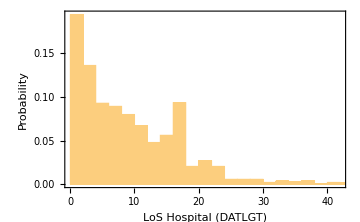

```mathematica
Histogram[DATLGT,Automatic,"Probability",Frame->True,FrameLabel->{"LoS Hospital (DATLGT)","Probability"},ImageSize->Medium]
```

```mathematica
Length/@{fHospAd,fHospDes} (*They have the same length due to DATDS is gotten joining the discharge variables to the whole set of cases *)
```

{1001,1001}

```mathematica
(************************************Testing**********)
```

```mathematica
DeleteCases[fHospToCRdischarge,""][[1;;6]]
```

<|caso1007→Mon 6 Apr 2020,caso1008→Wed 22 Apr 2020,caso1013→Fri 17 Apr 2020,caso1019→Mon 6 Apr 2020,caso1020→Thu 23 Apr 2020,caso1030→Mon 27 Apr 2020|>

```mathematica
DeleteCases[fHospToFdischarge,""][[1;;6]]
```

<|caso1041→Fri 10 Apr 2020,caso1058→Mon 6 Apr 2020,caso1132→Fri 3 Apr 2020,caso1200→Mon 6 Apr 2020,caso1203→Sat 4 Apr 2020,caso1238→Mon 6 Apr 2020|>

```mathematica
DeleteCases[fHospTpUCIdischarge,""][[1;;6]]
```

<|caso1032→Sat 4 Apr 2020,caso1040→Fri 17 Apr 2020,caso1052→Mon 6 Apr 2020,caso1062→Mon 6 Apr 2020,caso1093→Mon 6 Apr 2020,caso1133→Thu 16 Apr 2020|>

```mathematica
fHospDes[#]&/@{"caso1007","caso1041","caso1032"}
```

{Mon 6 Apr 2020,Fri 10 Apr 2020,Sat 4 Apr 2020}

#### UCI bed occupation data: DATADI/DATDSI/DATLGTI

```mathematica
DATADI=masterM[[1,#]]->adUCI[masterM[[All,{1,#}]]]&/@Range[2,10001(*Length[allMs[[-1]]]*)]//Association;(*Date of admission UCI*)
```

```mathematica
fUCIToCRdischarge=masterM[[1,#]]->fUCIToCR[masterM[[All,{1,#}]]]&/@Range[2,10001(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
fUCIToFdischarge=masterM[[1,#]]->fUCIToF[masterM[[All,{1,#}]]]&/@Range[2,10001(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
fUCIToHdischarge=masterM[[1,#]]->fUCIToH[masterM[[All,{1,#}]]]&/@Range[2,10001(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
DATDSI=Join[cases,DeleteCases[fUCIToCRdischarge,""],DeleteCases[fUCIToFdischarge,""],DeleteCases[fUCIToHdischarge,""]];(*Discharge from UCI*)
```

```mathematica
DATLGTI=DATDSI-DATADI(* Length of stay in UCI*);
```

```mathematica
Length/@{DATDSI,DATADI}
```

{10000,10000}

```mathematica
DATLGTI["caso999"](* This cases are those who do not have any date of admission and discharge*)
```

(<|caso1→Missing,caso2→Missing,caso3→Missing,caso4→Missing,caso5→Missing,caso6→Missing,caso7→Missing,caso8→Missing,caso9→Missing,caso10→Missing,caso11→Missing,9978,caso9990→Missing,caso9991→Missing,caso9992→Missing,caso9993→Missing,caso9994→Missing,caso9995→Missing,caso9996→Missing,caso9997→Missing,caso9998→Missing,caso9999→Missing,caso10000→Missing|>+<|1|>)[caso999]
 |  |  |  |

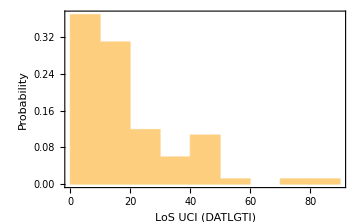

```mathematica
Histogram[DATLGTI,Automatic,"Probability",Frame->True,FrameLabel->{"LoS UCI (DATLGTI)","Probability"},ImageSize->Medium]
```

```mathematica
DATADIh=DateString/@(DATADI/.""->"Missing");DATADIh[[1;;10]]
DATDSIh=DateString/@DATDSI;DATDSIh[[1;;10]]
DATLGTIh=day/@(DATLGTI/.-""+"Missing"->"Missing");DATLGTIh[[1;;10]]
```

#### Calculating Yes/No for Admission: DSXHO / DSXIC

```mathematica
DSXHO=DATAD/.{""->"No",DateObject[___]->"Yes"};
```

```mathematica
DSXIC=DATADI/.{""->"No",DateObject[___]->"Yes"};
```

```mathematica
DSXHOh=DSXHO;DSXHOh[[1;;10]]
DSXICh=DSXIC;DSXICh[[1;;10]]
```

#### Calculating DATAD/DATDS

```mathematica
(********************Calculating DATAD y DATDS. Aqui se calculan las fechas de entrada y salida del hospital considerando UCI como parte de la entrada y salida PREGUNTAR!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!1)
```

```mathematica
(********************** Calculating Outcomes *)
```

```mathematica
(*ESTAS VARIABLES SON MEJOR CALCULARLAS EN dataArmonization.n*)
```

#### Calculating DSXOS/DATOS

```mathematica
fallecidos=masterM[[1,#]]->estFallecido[masterM[[All,{1,#}]]]&/@Range[2,10001]//Association;
```

```mathematica
recuperado=masterM[[1,#]]->estRecuperado[masterM[[All,{1,#}]]]&/@Range[2,10001]//Association;
```

```mathematica
DSXOS=Join[cases,DeleteCases[fallecidos,"Missing"],DeleteCases[recuperado,"Missing"]];(* Outcome status: Recovered/Deceased *)
```

```mathematica
fallecidos[[100;;160]]
```

<|caso1098→Missing,caso1099→Missing,caso1100→Missing,caso1101→Missing,caso1102→Missing,caso1103→Missing,caso1104→Missing,caso1105→Missing,caso1106→Missing,caso1107→Missing,caso1108→Missing,caso1109→Missing,caso1110→Missing,caso1111→Missing,caso1112→Missing,caso1113→Missing,caso1114→Missing,caso1115→Missing,caso1116→Missing,caso1117→Missing,caso1118→Missing,caso1119→Missing,caso1120→Missing,caso1121→Missing,caso1122→Missing,caso1123→Missing,caso1124→Missing,caso1125→Missing,caso1126→Missing,caso1127→Missing,caso1128→Missing,caso1129→Missing,caso1130→Missing,caso1131→Missing,caso1132→Fallecido,caso1133→Missing,caso1134→Missing,caso1135→Missing,caso1136→Missing,caso1137→Missing,caso1138→Missing,caso1139→Missing,caso1140→Missing,caso1141→Missing,caso1142→Missing,caso1143→Missing,caso1144→Missing,caso1145→Missing,caso1146→Missing,caso1147→Missing,caso1148→Missing,caso1149→Missing,caso1150→Fallecido,caso1151→Missing,caso1152→Missing,caso1153→Missing,caso1154→Missing,caso1155→Missing,caso1156→Missing,caso1157→Missing,caso1158→Missing|>

```mathematica
fallecidos["caso1150"]
```

Fallecido

```mathematica
recuperado["caso1150"]
```

Missing

```mathematica
DSXOS["caso1150"]
```

Fallecido

```mathematica
(*************************)
```

```mathematica
fallecidosD=masterM[[1,#]]->feFallecido[masterM[[All,{1,#}]]]&/@Range[2,10001]//Association;
```

```mathematica
recuperadoD=masterM[[1,#]]->feRecuperado[masterM[[All,{1,#}]]]&/@Range[2,10001]//Association;
```

```mathematica
fallecidosD[[1;;6]]
```

```mathematica
<|"caso999"->"","caso1000"->"","caso1001"->"","caso1002"->"","caso1003"->"","caso1004"->""|>
```

```mathematica
DATOS=Join[cases,DeleteCases[fallecidosD,""],DeleteCases[recuperadoD,""]];(* Outcome status: Recovered/Deceased *)
```

```mathematica
fallecidosD["caso1150"]
```

Wed 29 Apr 2020

```mathematica
recuperadoD["caso1150"]
```

```mathematica
DATOS["caso1150"]
```

Wed 29 Apr 2020

```mathematica
DSXOSh=(DSXOS/.{"Recuperado (Hospital)"->"Recovered","Recuperado"->"Recovery","recuperado"->"Recovery","fallecido"->"Deceased","Fallecido"->"Deceased"});DSXOSh[[1;;10]]
DATOSh=DateString/@DATOS;DATOSh[[1;;10]]
```

#### Fusion of the variables

```mathematica
hospitalKeys={"Hospital","hospital","Recuperado (Hospital)","HOSPITAL","Hospital  ","Hospital   ","Hospital "};
uciKeys={"Hospital UCI","hospital UCI","Hospital UCI ","HOSPITAL UCI"};
recuperadoCasaKeys={"En casa","Casa","casa","recuperado","Recuperado","Casa  ","CASA","Casa ","Casa                                                                                                                                                                                                    "};
fallecidoKeys={"fallecido","Fallecido"};
```

```mathematica
(* Estoy poniendo Missing cuando no hay datos porque no esta en la base de datos quiza porque no ingresa a UCI o Hopsital o porque no se reportó el dato*)
```

```mathematica
$DateStringFormat={"Day","/","Month","/","Year"};(* Esto cambia el formato default del DateString *)
```

```mathematica
DATADh=DateString/@(DATAD/.""->"Missing");DATADh[[1;;10]]
DATDSh=DateString/@DATDS;DATDSh[[1;;10]]
DATLGTh=day/@(DATLGT/.-""+"Missing"->"Missing");DATLGTh[[1;;10]]
```

```mathematica
casesN=Range[1,10000];
```

```mathematica
dataBase={{"ID","DATAD","DATDS","DATLGT","DSXHO","DATADI","DATDSI","DATLGTI","DSXIC","DSXOS","DATOS"},Sequence@@Transpose[{casesN,DATADh//Values,DATDSh//Values,DATLGTh//Values,DSXHOh//Values,DATADIh//Values,DATDSIh//Values,DATLGTIh//Values,DSXICh//Values,DSXOSh//Values,DATOSh//Values}]};
```

```mathematica
Export["dataBase2-1.csv",dataBase,"CSV"]
```

dataBase2-1.csv

```mathematica
DateObject[{2020,4,6},"Day","Gregorian",-5.]//DateString
```

Mon 6 Apr 2020

```mathematica
{DateObject[{2020,4,6},"Day","Gregorian",-5.],"",DateObject[{2020,4,6},"Day","Gregorian",-5.]}//DateString
```

DateString::arg: Argument {DateObject[{2020,4,6},Day,Gregorian,-5.],,DateObject[{2020,4,6},Day,Gregorian,-5.]} cannot be interpreted as a date or time input or as a date string format.

DateString[{Mon 6 Apr 2020,,Mon 6 Apr 2020}]

```mathematica
"caso1006"->day["Missing"]
```

```mathematica
"Miissng"//DateString
```

Miissng

```mathematica
Quantity[18, "Days"][[1]]
```

```mathematica
18
```

```mathematica
Quantity[18, "Days"]//Normalize
```

1

```mathematica
"Mon 6 Apr 2020"
```

```mathematica
Clear[day]
```

```mathematica
day["Missing"]:="Missing"
day[quantity_/;Head[quantity]==Quantity]:=QuantityMagnitude[quantity]
```

```mathematica
f[""]:=d
```

```mathematica
f[""]
```

d

```mathematica
"caso1006"->day["Missing"]
```

caso1006→day[Missing]

```mathematica
day["Miissng"]
```

Miissng

```mathematica
"Missing"
```

```mathematica
MatchQ[Quantity[18, "Days"],Quantity]
```

False

```mathematica
Quantity[18, "Days"]//Head
```

Quantity

### Reviewing the analysis

```mathematica
fecha[[210]]
```

2020-09-24

```mathematica
d1=Import["2020-09-24.xlsx"];(* Este es la base control con la cual se revisará si la matrix esta bien hecha. Haciendo uso de las columnas Fecha-muerte y Fecha-recuperación*)
```

```mathematica
d1//Dimensions
```

{1,790824,22}

```mathematica
d1[[1,1]]
```

{Caso,Fecha Not,Departamento,nombre_depa,Ciudad_municipio,nombre_mun,Edad,Sexo,Fuente_tipo_contagio,Ubicacion,Estado,Pais_viajo_1_cod,Pais_viajo_1_nom,Fecha_inicio_sintomas,Fecha_muerte,Fecha_diagnostico,Fecha_recuperado,Fecha cargue web,Ubicacion,Tipo_recuperacion,per_etn_2,nom_grupo_}

```mathematica
fRecuperadoControl=Transpose[{d1[[1,All,1]],d1[[1,All,-6]]}];
```

```mathematica
fFallecidoControl=Transpose[{d1[[1,All,1]],d1[[1,All,-8]]}];
```

#### Comparison with death date part 1

Here it is compared with the result of the H->F & UCI-> F paths, only the 1878 case

```mathematica
fHospToFd=masterM[[1,#]]->fHospToF[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
fUCIToFd=masterM[[1,#]]->fUCIToF[masterM[[All,{1,#}]]]&/@Range[1000,2000(*Length[allMs[[-1]]]*)]//Association;
```

```mathematica
DeleteCases[fHospToFd,Missing["NotFound"]][[All,2,1]]
```

Part::partd: Part specification «1» is longer than depth of object.

```mathematica
DeleteCases[fUCIToFd,Missing["NotFound"]][[All,2,1]]
```

Part::partd: Part specification «1» is longer than depth of object.

<|caso999→,caso1000→,caso1001→,caso1002→,caso1003→,caso1004→,caso1005→,caso1006→,caso1007→,caso1008→,caso1009→,caso1010→,caso1011→,caso1012→,caso1013→,caso1014→,caso1015→,caso1016→,caso1017→,caso1018→,caso1019→,caso1020→,caso1021→,caso1022→,caso1023→,caso1024→,caso1025→,caso1026→,caso1027→,caso1028→,caso1029→,caso1030→,caso1031→,caso1032→Tue 14 Apr 2020,caso1033→,caso1034→,caso1035→,caso1036→,caso1037→,caso1038→,caso1039→,caso1040→Mon 20 Apr 2020,caso1041→,caso1042→,caso1043→,caso1044→,caso1045→,caso1046→,caso1047→,caso1048→,caso1049→,caso1050→,caso1051→,caso1052→Mon 20 Apr 2020,caso1053→,caso1054→,caso1055→,caso1056→,caso1057→,caso1058→,caso1059→,caso1060→,caso1061→,caso1062→Wed 22 Apr 2020,caso1063→,caso1064→Sun 12 Apr 2020,caso1065→,caso1066→,caso1067→,caso1068→,caso1069→,caso1070→,caso1071→,caso1072→,caso1073→,caso1074→,caso1075→,caso1076→,caso1077→,caso1078→,caso1079→,caso1080→,caso1081→,caso1082→,caso1083→,caso1084→,caso1085→,caso1086→,caso1087→,caso1088→,caso1089→,caso1090→,caso1091→,caso1092→,caso1093→,caso1094→,caso1095→,caso1096→Sun 12 Apr 2020,caso1097→,caso1098→,caso1099→,caso1100→,caso1101→,caso1102→,caso1103→,caso1104→,caso1105→,caso1106→,caso1107→,caso1108→,caso1109→,caso1110→,caso1111→,caso1112→,caso1113→,caso1114→,caso1115→,caso1116→,caso1117→,caso1118→,caso1119→,caso1120→,caso1121→,caso1122→,caso1123→,caso1124→,caso1125→,caso1126→,caso1127→,caso1128→,caso1129→,caso1130→,caso1131→,caso1132→,caso1133→,caso1134→,caso1135→,caso1136→,caso1137→,caso1138→,caso1139→,caso1140→,caso1141→,caso1142→,caso1143→,caso1144→,caso1145→,caso1146→,caso1147→,caso1148→,caso1149→,caso1150→Wed 29 Apr 2020,caso1151→,caso1152→,caso1153→,caso1154→,caso1155→,caso1156→,caso1157→,caso1158→,caso1159→,caso1160→,caso1161→,caso1162→,caso1163→,caso1164→Wed 15 Apr 2020,caso1165→,caso1166→,caso1167→,caso1168→,caso1169→,caso1170→Tue 7 Apr 2020,caso1171→,caso1172→,caso1173→,caso1174→,caso1175→,caso1176→,caso1177→,caso1178→,caso1179→Wed 6 May 2020,caso1180→,caso1181→,caso1182→,caso1183→,caso1184→,caso1185→,caso1186→,caso1187→,caso1188→,caso1189→,caso1190→,caso1191→,caso1192→,caso1193→,caso1194→,caso1195→,caso1196→,caso1197→,caso1198→,caso1199→,caso1200→,caso1201→,caso1202→,caso1203→,caso1204→,caso1205→,caso1206→,caso1207→,caso1208→,caso1209→,caso1210→,caso1211→,caso1212→,caso1213→,caso1214→,caso1215→,caso1216→,caso1217→,caso1218→,caso1219→,caso1220→,caso1221→,caso1222→,caso1223→,caso1224→,caso1225→,caso1226→,caso1227→,caso1228→,caso1229→,caso1230→,caso1231→,caso1232→,caso1233→,caso1234→,caso1235→,caso1236→,caso1237→,caso1238→,caso1239→,caso1240→,caso1241→,caso1242→,caso1243→,caso1244→,caso1245→,caso1246→,caso1247→,caso1248→,caso1249→,caso1250→,caso1251→,caso1252→,caso1253→,caso1254→,caso1255→,caso1256→,caso1257→,caso1258→,caso1259→,caso1260→,caso1261→,caso1262→,caso1263→,caso1264→,caso1265→,caso1266→,caso1267→,caso1268→,caso1269→Sat 18 Apr 2020,caso1270→,caso1271→,caso1272→,caso1273→,caso1274→,caso1275→,caso1276→,caso1277→,caso1278→,caso1279→,caso1280→,caso1281→,caso1282→,caso1283→,caso1284→,caso1285→,caso1286→,caso1287→,caso1288→,caso1289→,caso1290→,caso1291→,caso1292→,caso1293→,caso1294→,caso1295→,caso1296→,caso1297→,caso1298→,caso1299→,caso1300→,caso1301→,caso1302→,caso1303→,caso1304→,caso1305→,caso1306→,caso1307→,caso1308→,caso1309→,caso1310→,caso1311→,caso1312→,caso1313→,caso1314→,caso1315→,caso1316→,caso1317→,caso1318→,caso1319→,caso1320→,caso1321→,caso1322→,caso1323→,caso1324→,caso1325→,caso1326→,caso1327→,caso1328→,caso1329→,caso1330→,caso1331→,caso1332→,caso1333→,caso1334→,caso1335→,caso1336→,caso1337→,caso1338→,caso1339→,caso1340→,caso1341→,caso1342→,caso1343→,caso1344→,caso1345→,caso1346→,caso1347→,caso1348→,caso1349→,caso1350→,caso1351→,caso1352→,caso1353→,caso1354→,caso1355→,caso1356→,caso1357→,caso1358→,caso1359→,caso1360→,caso1361→,caso1362→,caso1363→,caso1364→Thu 16 Apr 2020,caso1365→,caso1366→,caso1367→,caso1368→,caso1369→,caso1370→,caso1371→,caso1372→Mon 6 Apr 2020,caso1373→,caso1374→,caso1375→,caso1376→,caso1377→,caso1378→,caso1379→,caso1380→,caso1381→,caso1382→,caso1383→,caso1384→,caso1385→,caso1386→,caso1387→,caso1388→,caso1389→,caso1390→,caso1391→,caso1392→,caso1393→,caso1394→,caso1395→,caso1396→,caso1397→,caso1398→,caso1399→,caso1400→,caso1401→,caso1402→,caso1403→,caso1404→,caso1405→,caso1406→,caso1407→,caso1408→,caso1409→,caso1410→,caso1411→,caso1412→,caso1413→,caso1414→,caso1415→,caso1416→,caso1417→,caso1418→,caso1419→,caso1420→,caso1421→,caso1422→,caso1423→,caso1424→,caso1425→,caso1426→,caso1427→,caso1428→,caso1429→,caso1430→,caso1431→,caso1432→Tue 21 Apr 2020,caso1433→,caso1434→,caso1435→,caso1436→,caso1437→,caso1438→,caso1439→,caso1440→,caso1441→,caso1442→,caso1443→,caso1444→,caso1445→,caso1446→,caso1447→,caso1448→,caso1449→,caso1450→,caso1451→,caso1452→,caso1453→,caso1454→,caso1455→,caso1456→,caso1457→,caso1458→,caso1459→,caso1460→,caso1461→,caso1462→,caso1463→Tue 14 Apr 2020,caso1464→,caso1465→,caso1466→,caso1467→,caso1468→,caso1469→,caso1470→,caso1471→,caso1472→,caso1473→,caso1474→,caso1475→,caso1476→,caso1477→,caso1478→,caso1479→,caso1480→Wed 29 Apr 2020,caso1481→,caso1482→,caso1483→,caso1484→,caso1485→,caso1486→Thu 9 Apr 2020,caso1487→Sun 26 Apr 2020,caso1488→,caso1489→,caso1490→,caso1491→,caso1492→,caso1493→,caso1494→,caso1495→,caso1496→,caso1497→,caso1498→,caso1499→,caso1500→,caso1501→,caso1502→,caso1503→,caso1504→,caso1505→,caso1506→,caso1507→,caso1508→,caso1509→,caso1510→,caso1511→,caso1512→,caso1513→,caso1514→,caso1515→,caso1516→,caso1517→,caso1518→,caso1519→,caso1520→,caso1521→,caso1522→,caso1523→,caso1524→,caso1525→,caso1526→,caso1527→,caso1528→,caso1529→,caso1530→,caso1531→,caso1532→Thu 16 Apr 2020,caso1533→,caso1534→,caso1535→,caso1536→,caso1537→,caso1538→,caso1539→,caso1540→,caso1541→,caso1542→,caso1543→,caso1544→,caso1545→,caso1546→,caso1547→,caso1548→,caso1549→,caso1550→,caso1551→,caso1552→,caso1553→,caso1554→,caso1555→,caso1556→,caso1557→,caso1558→,caso1559→,caso1560→,caso1561→,caso1562→,caso1563→,caso1564→,caso1565→,caso1566→,caso1567→,caso1568→,caso1569→,caso1570→,caso1571→,caso1572→,caso1573→,caso1574→,caso1575→,caso1576→,caso1577→,caso1578→,caso1579→,caso1580→,caso1581→,caso1582→,caso1583→,caso1584→,caso1585→,caso1586→,caso1587→,caso1588→,caso1589→,caso1590→,caso1591→,caso1592→,caso1593→,caso1594→,caso1595→,caso1596→,caso1597→,caso1598→,caso1599→,caso1600→,caso1601→,caso1602→,caso1603→,caso1604→,caso1605→,caso1606→,caso1607→,caso1608→,caso1609→,caso1610→,caso1611→,caso1612→,caso1613→,caso1614→,caso1615→,caso1616→,caso1617→,caso1618→,caso1619→,caso1620→,caso1621→,caso1622→,caso1623→,caso1624→,caso1625→,caso1626→,caso1627→,caso1628→,caso1629→,caso1630→,caso1631→,caso1632→,caso1633→,caso1634→,caso1635→,caso1636→,caso1637→,caso1638→,caso1639→,caso1640→,caso1641→,caso1642→,caso1643→,caso1644→,caso1645→,caso1646→,caso1647→,caso1648→,caso1649→,caso1650→,caso1651→,caso1652→,caso1653→,caso1654→,caso1655→,caso1656→,caso1657→,caso1658→,caso1659→,caso1660→,caso1661→,caso1662→,caso1663→,caso1664→,caso1665→,caso1666→,caso1667→Tue 14 Apr 2020,caso1668→,caso1669→,caso1670→,caso1671→,caso1672→,caso1673→,caso1674→,caso1675→,caso1676→,caso1677→,caso1678→,caso1679→,caso1680→,caso1681→,caso1682→,caso1683→,caso1684→,caso1685→,caso1686→,caso1687→,caso1688→Sat 2 May 2020,caso1689→,caso1690→,caso1691→,caso1692→,caso1693→Mon 4 May 2020,caso1694→,caso1695→,caso1696→,caso1697→,caso1698→Wed 3 Jun 2020,caso1699→,caso1700→,caso1701→,caso1702→,caso1703→,caso1704→,caso1705→,caso1706→,caso1707→,caso1708→,caso1709→,caso1710→,caso1711→,caso1712→,caso1713→,caso1714→,caso1715→,caso1716→,caso1717→,caso1718→,caso1719→,caso1720→,caso1721→,caso1722→,caso1723→,caso1724→,caso1725→,caso1726→,caso1727→,caso1728→,caso1729→,caso1730→,caso1731→,caso1732→Wed 15 Apr 2020,caso1733→,caso1734→,caso1735→,caso1736→,caso1737→,caso1738→,caso1739→,caso1740→,caso1741→,caso1742→,caso1743→,caso1744→,caso1745→,caso1746→,caso1747→,caso1748→,caso1749→,caso1750→,caso1751→,caso1752→Thu 30 Apr 2020,caso1753→,caso1754→,caso1755→,caso1756→,caso1757→,caso1758→,caso1759→,caso1760→,caso1761→,caso1762→,caso1763→,caso1764→,caso1765→,caso1766→,caso1767→,caso1768→,caso1769→,caso1770→,caso1771→,caso1772→,caso1773→,caso1774→,caso1775→,caso1776→,caso1777→,caso1778→,caso1779→,caso1780→,caso1781→,caso1782→,caso1783→,caso1784→,caso1785→,caso1786→,caso1787→,caso1788→,caso1789→,caso1790→,caso1791→,caso1792→,caso1793→,caso1794→,caso1795→,caso1796→,caso1797→,caso1798→,caso1799→,caso1800→,caso1801→,caso1802→,caso1803→,caso1804→,caso1805→,caso1806→,caso1807→,caso1808→,caso1809→,caso1810→,caso1811→,caso1812→,caso1813→,caso1814→,caso1815→,caso1816→,caso1817→,caso1818→,caso1819→,caso1820→,caso1821→,caso1822→,caso1823→,caso1824→Thu 16 Apr 2020,caso1825→,caso1826→,caso1827→,caso1828→,caso1829→,caso1830→,caso1831→,caso1832→,caso1833→,caso1834→,caso1835→,caso1836→,caso1837→,caso1838→,caso1839→,caso1840→,caso1841→,caso1842→,caso1843→,caso1844→,caso1845→,caso1846→,caso1847→,caso1848→,caso1849→Sun 12 Apr 2020,caso1850→,caso1851→,caso1852→,caso1853→,caso1854→,caso1855→,caso1856→,caso1857→,caso1858→,caso1859→,caso1860→,caso1861→,caso1862→,caso1863→,caso1864→,caso1865→,caso1866→,caso1867→Thu 16 Apr 2020,caso1868→,caso1869→,caso1870→,caso1871→,caso1872→,caso1873→,caso1874→,caso1875→,caso1876→,caso1877→,caso1878→,caso1879→,caso1880→,caso1881→,caso1882→,caso1883→,caso1884→,caso1885→,caso1886→,caso1887→,caso1888→,caso1889→,caso1890→,caso1891→,caso1892→,caso1893→,caso1894→,caso1895→,caso1896→,caso1897→,caso1898→,caso1899→,caso1900→,caso1901→,caso1902→,caso1903→,caso1904→,caso1905→,caso1906→,caso1907→,caso1908→,caso1909→,caso1910→,caso1911→,caso1912→,caso1913→,caso1914→,caso1915→Fri 10 Apr 2020,caso1916→,caso1917→,caso1918→,caso1919→,caso1920→,caso1921→,caso1922→,caso1923→,caso1924→,caso1925→,caso1926→,caso1927→,caso1928→Sun 12 Apr 2020,caso1929→Sun 12 Apr 2020,caso1930→,caso1931→,caso1932→,caso1933→,caso1934→,caso1935→,caso1936→,caso1937→,caso1938→,caso1939→,caso1940→,caso1941→,caso1942→,caso1943→,caso1944→,caso1945→,caso1946→,caso1947→,caso1948→,caso1949→,caso1950→,caso1951→,caso1952→,caso1953→,caso1954→,caso1955→,caso1956→,caso1957→,caso1958→,caso1959→,caso1960→,caso1961→,caso1962→,caso1963→,caso1964→,caso1965→,caso1966→,caso1967→,caso1968→,caso1969→,caso1970→,caso1971→,caso1972→,caso1973→,caso1974→,caso1975→,caso1976→,caso1977→,caso1978→,caso1979→,caso1980→,caso1981→,caso1982→,caso1983→,caso1984→,caso1985→,caso1986→,caso1987→,caso1988→,caso1989→,caso1990→,caso1991→,caso1992→,caso1993→,caso1994→,caso1995→,caso1996→,caso1997→,caso1998→,caso1999→|>⟦All,2,1⟧

```mathematica
fallecidoDataControl=AssociationThread[#[[All,1]],#[[All,2]]]&@fFallecidoControl[[1000;;2000]];
```

```mathematica
masterM[[All,{1,1879}]]
```

{{fecha,caso1878},{2020-03-15,},{2020-03-16,},{2020-03-17,},{2020-03-18,},{2020-03-19,},{2020-03-20,},{2020-03-21,},{2020-03-22,},{2020-03-23,},{2020-03-24,},{2020-03-25,},{2020-03-26,},{2020-03-27,},{2020-03-28,},{2020-03-29,},{2020-03-30,},{2020-03-31,},{2020-04-01,},{2020-04-02,},{2020-04-03,},{2020-04-04,},{2020-04-05,},{2020-04-06,},{2020-04-07,},{2020-04-08,Hospital},{2020-04-09,Hospital},{2020-04-10,Hospital},{2020-04-12,Fallecido},{2020-04-13,Fallecido},{2020-04-14,Fallecido},{2020-04-15,Fallecido},{2020-04-16,Fallecido},{2020-04-17,Fallecido},{2020-04-18,Fallecido},{2020-04-19,Fallecido},{2020-04-20,Fallecido},{2020-04-21,Fallecido},{2020-04-22,Fallecido},{2020-04-23,Fallecido},{2020-04-24,Fallecido},{2020-04-25,Fallecido},{2020-04-26,Fallecido},{2020-04-27,Fallecido},{2020-04-28,Fallecido},{2020-04-29,Fallecido},{2020-04-30,Fallecido},{2020-05-01,Fallecido},{2020-05-02,Fallecido},{2020-05-03,Fallecido},{2020-05-04,Fallecido},{2020-05-05,Fallecido},{2020-05-06,Fallecido},{2020-05-07,Fallecido},{2020-05-08,Fallecido},{2020-05-09,Fallecido},{2020-05-10,Fallecido},{2020-05-11,Fallecido},{2020-05-12,Fallecido},{2020-05-13,Fallecido},{2020-05-14,Fallecido},{2020-05-15,Fallecido},{2020-05-16,Fallecido},{2020-05-17,Fallecido},{2020-05-18,Fallecido},{2020-05-19,Fallecido},{2020-05-20,Fallecido},{2020-05-21,Fallecido},{2020-05-22,Fallecido},{2020-05-23,Fallecido},{2020-05-24,Fallecido},{2020-05-25,Fallecido},{2020-05-26,Fallecido},{2020-05-27,Fallecido},{2020-05-28,Fallecido},{2020-05-29,Fallecido},{2020-05-30,Fallecido},{2020-05-31,Fallecido},{2020-06-01,Fallecido},{2020-06-02,Fallecido},{2020-06-03,Fallecido},{2020-06-04,Fallecido},{2020-06-05,Fallecido},{2020-06-06,Fallecido},{2020-06-07,Fallecido},{2020-06-08,Fallecido},{2020-06-09,Fallecido},{2020-06-10,Fallecido},{2020-06-11,Fallecido},{2020-06-12,Fallecido},{2020-06-13,Fallecido},{2020-06-14,Fallecido},{2020-06-15,Fallecido},{2020-06-16,Fallecido},{2020-06-17,Fallecido},{2020-06-18,Fallecido},{2020-06-19,Fallecido},{2020-06-20,Fallecido},{2020-06-21,Fallecido},{2020-06-22,Fallecido},{2020-06-23,Fallecido},{2020-06-24,Fallecido},{2020-06-25,Fallecido},{2020-06-26,Fallecido},{2020-06-27,Fallecido},{2020-06-28,Fallecido},{2020-06-29,Fallecido},{2020-06-30,Fallecido},{2020-07-01,Fallecido},{2020-07-02,Fallecido},{2020-07-03,Fallecido},{2020-07-04,Fallecido},{2020-07-05,Fallecido},{2020-07-06,Fallecido},{2020-07-07,Fallecido},{2020-07-08,Fallecido},{2020-07-09,Fallecido},{2020-07-10,Fallecido},{2020-07-11,Fallecido},{2020-07-12,Fallecido},{2020-07-13,Fallecido},{2020-07-14,Fallecido},{2020-07-15,Fallecido},{2020-07-16,Fallecido},{2020-07-17,Fallecido},{2020-07-18,Fallecido},{2020-07-19,Fallecido},{2020-07-20,Fallecido},{2020-07-21,Fallecido},{2020-07-22,Fallecido},{2020-07-23,Fallecido},{2020-07-24,Fallecido},{2020-07-25,Fallecido},{2020-07-26,Fallecido},{2020-07-27,Fallecido},{2020-07-28,Fallecido},{2020-07-29,Fallecido},{2020-07-30,Fallecido},{2020-07-31,Fallecido},{2020-08-01,Fallecido},{2020-08-02,Fallecido},{2020-08-03,Fallecido},{2020-08-04,Fallecido},{2020-08-05,Fallecido},{2020-08-06,Fallecido},{2020-08-07,Fallecido},{2020-08-08,Fallecido},{2020-08-09,Fallecido},{2020-08-10,Fallecido},{2020-08-11,Fallecido},{2020-08-12,Fallecido},{2020-08-13,Fallecido},{2020-08-14,Fallecido},{2020-08-15,Fallecido},{2020-08-16,Fallecido},{2020-08-17,Fallecido},{2020-08-18,Fallecido},{2020-08-19,Fallecido},{2020-08-20,Fallecido},{2020-08-21,Fallecido},{2020-08-22,Fallecido},{2020-08-23,Fallecido},{2020-08-24,Fallecido},{2020-08-25,Fallecido},{2020-08-26,Fallecido},{2020-08-27,Fallecido},{2020-08-28,Fallecido},{2020-08-29,Fallecido},{2020-08-30,Fallecido},{2020-08-31,Fallecido},{2020-09-01,Fallecido},{2020-09-02,Fallecido},{2020-09-03,Fallecido},{2020-09-04,Fallecido},{2020-09-05,Fallecido},{2020-09-06,Fallecido},{2020-09-07,Fallecido},{2020-09-08,Fallecido},{2020-09-09,Fallecido},{2020-09-10,Fallecido},{2020-09-11,Fallecido},{2020-09-12,Fallecido},{2020-09-13,Fallecido},{2020-09-14,Fallecido},{2020-09-15,Fallecido},{2020-09-16,Fallecido},{2020-09-17,Fallecido},{2020-09-18,Fallecido},{2020-09-19,Fallecido},{2020-09-20,Fallecido},{2020-09-21,Fallecido},{2020-09-22,Fallecido},{2020-09-23,Fallecido},{2020-09-24,Fallecido},{2020-09-25,Fallecido},{2020-09-26,Fallecido},{2020-09-27,Fallecido},{2020-09-28,Fallecido},{2020-09-29,Fallecido},{2020-09-30,Fallecido},{2020-10-01,Fallecido},{2020-10-02,Fallecido},{2020-10-03,Fallecido}}

```mathematica
(*Revisando caso 1878: Aparece fallecido 4 abril en la data del 2020-09-24 pero en mi matrix sale muerto el 12 de abril y el cuatro no registra Ubicación*)
```

```mathematica
caso1878=Import["2020-04-04.xlsx"];
```

```mathematica
caso1878//Dimensions
```

{1,1449,10}

```mathematica
caso1878[[1879]]
```

Part::partw: Part 1879 of {{{Caso,Fecha Not,Departamento,Ciudad,Edad,Sexo,Tipo,Ubicación,Estado,Pais de procedencia},{1.,DateObject[{2020,3,6,0,0,0.},Instant,Gregorian,-5.],Bogotá, D.C.,Bogotá,19.,F,Importado,Recuperado,Leve,Italia},«7»,{9.,DateObject[{2020,3,11,0,0,0.},Instant,Gregorian,-5.],Bogotá, D.C.,Bogotá,28.,F,Importado,Recuperado,Leve,España},«1439»}} does not exist.

{{{Caso,Fecha Not,Departamento,Ciudad,Edad,Sexo,Tipo,Ubicación,Estado,Pais de procedencia},{1.,Fri 6 Mar 2020 00:00:00GMT-5,Bogotá, D.C.,Bogotá,19.,F,Importado,Recuperado,Leve,Italia},{2.,Mon 9 Mar 2020 00:00:00GMT-5,Valle del Cauca,Buga,34.,M,Importado,Recuperado,Leve,España},1443,{,,,,,,,,,},{,,,,,,,,,},{,,,,,,,,,}}}⟦1879⟧
 |  |  |  |

```mathematica
(****CONCLUSION)
```

1. The 1879 case was not in the 2020-04-04 database. According with masterM he is reported in 2020-04-08 in the Hospital. However, the column “Fecha-muerte” from the 2020-09-24 database reported him as dead in April 4 2020.
2. Some errors of the analysis comes from the delay in report. For instance, someone gets in the database in 4 April 2020 and it is reported as in Hospital. However, it could be in the hospital some days ago, then the matrix will assume  it as admission date the day in which it gets in the database

```mathematica
(******************************************************************************************************************)
```

#### Comparison with death date part2

```mathematica
(*A ESTOS DE SE LE APLICA LAS FUNCIONES CON OUTPUT {date, Location}*)
```

Here it is compared with the result of the H->F & UCI-> F paths, by chunks of 1000 cases

```mathematica
fHospToFd=masterM[[1,#]]->fHospToF[masterM[[All,{1,#}]]]&/@Range[10000,11000]//Association;
```

```mathematica
fUCIToFd=masterM[[1,#]]->fUCIToF[masterM[[All,{1,#}]]]&/@Range[10000,11000]//Association;
```

```mathematica
fallecidoMaterM=Join[Join[AssociationThread[Table["caso"<>ToString@i,{i,9999,10999}]->""],DeleteCases[fHospToFd,Missing["NotFound"]][[All,2,1]]],DeleteCases[fUCIToFd,Missing["NotFound"]][[All,2,1]]];
```

```mathematica
fallecidoDataControl=AssociationThread[#[[All,1]],#[[All,2]]]&@fFallecidoControl[[10000;;11000]];
```

```mathematica
Length/@{fallecidoMaterM,fallecidoDataControl}
```

{1001,1001}

```mathematica
dataset=Dataset[<|"colMasterM"->#[[1]],"colControl"->#[[2]]|>&/@Transpose[{fallecidoMaterM//Values,fallecidoDataControl//Values}]]
```

```mathematica
Export["comparacion10000-11000casosFallecidos.m",dataset]
```

comparacion10000-11000casosFallecidos.m

#### Comparison with death date part 3

```mathematica
(*A ESTOS DE SE LE APLICA LAS FUNCIONES CON OUTPUT Date *)
```

Here it is used the complete reported dead

```mathematica
(********************convirtiendo las fechas a DateObject*)
```

```mathematica
fFallecido[[1033,2]]
```

Part::partd: Part specification fFallecido⟦1033,2⟧ is longer than depth of object.

fFallecido⟦1033,2⟧

```mathematica
DateObject[{2020,4,10,0,0,0.},"Instant","Gregorian",-5.]//InputForm
```

DateObject[{2020, 4, 10, 0, 0, 0.}, "Instant", "Gregorian", -5.]

```mathematica
fFallecido[[1042,2]]
```

Thu 9 Apr 2020 00:00:00GMT-5

```mathematica
fFallecido[[1033,2]]-fFallecido[[1042,2]]
```

1. days

```mathematica
fFallecidod[[34]]
```

2020-04-14

```mathematica
DateObject["2020-05-14"]
```

Thu 14 May 2020

```mathematica
DateObject["2020-05-14"]-fFallecido[[1042,2]]
```

35. days

```mathematica
(*****Tanto la data control como la matriz tienen los casos en las misma posiciones. Por eso omito la clave que refiere al caso)
```

```mathematica
Clear[toDataObject]
```

```mathematica
toDataObject["NotFound"]:="2"(*se pone 10 para que la resta con el control de -10 e identificar esto como la barra de los  casos sin fecha. IGUAL NO IMPORTA PORQUE EL HISTOGRAMA NO GRAFICA LOS STRINGS*)
toDataObject[date_]:=DateObject[date]
```

```mathematica
fallecidoDataControl=fFallecidoControl[[1000;;100000,2]];
```

```mathematica
fFallecidod=feFallecido[masterM[[All,{1,#}]]]&/@Range[1000,100000];
```

```mathematica
Histogram[fallecidoDataControl-fFallecidod,Automatic,"Probability",Frame->True,FrameLabel->{"Reported minus calculated dates","PDF"},ImageSize->Medium,PlotLabel->"100 000 cases"]
```

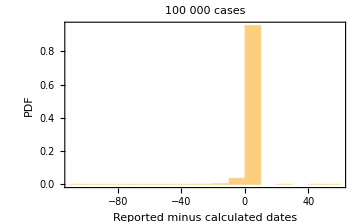
```mathematica
-Graphics-(*Con la matrizM corregida por los casos perdidos *)
```

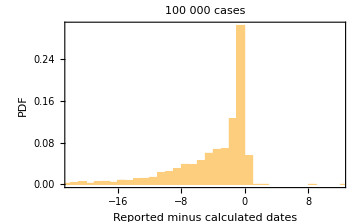

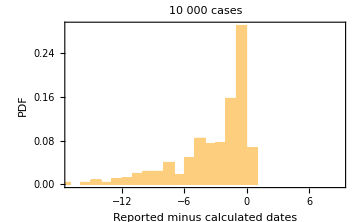

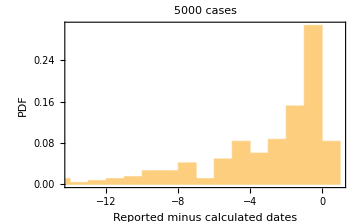

The matrix estimated reported higher dates than the database control

```mathematica
(**************************************************************)
```

#### Comparison with recuperated date

```mathematica
(*A ESTOS DE SE LE APLICA LAS FUNCIONES CON OUTPUT Date *)
```

```mathematica
RecuperadoDataControl=fRecuperadoControl[[1000;;5000,2]];
```

```mathematica
fRecuperado=feRecuperado[masterM[[All,{1,#}]]]&/@Range[1000,5000];(*Fecha de recuperados segun la matriz estimada*)
```

```mathematica
Histogram[RecuperadoDataControl-fRecuperado,Automatic,"Probability",Frame->True,FrameLabel->{"Reported minus calculated dates","PDF"},ImageSize->Medium,PlotLabel->"4 000 cases"]
```

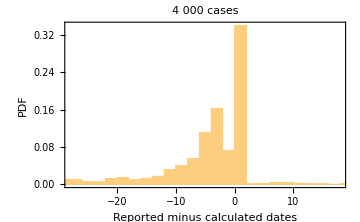
```mathematica
-Graphics-(*Con la matrizM corregida por los casos perdidos *)
```

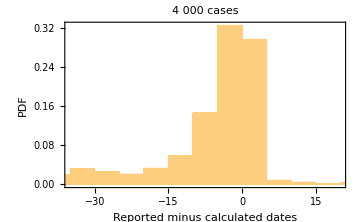

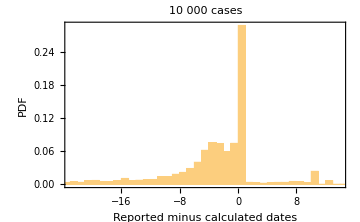

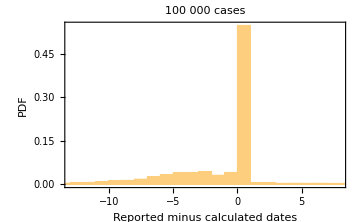

```mathematica
Count[RecuperadoDataControl-fRecuperado,Quantity[0., "Days"]]
```

1091

$Aborted

3. We can get the Dead/Recuperate date and compare them with the columns of the MAIN database (i.e. de most recent publicated .csv) to confirm it is well calculated

```mathematica
(*NOTA:  Para identificar que esto esta bien podriamos tomar 10 casos aleatorios y revisar cada uno para saber si cohinciden las fechas*)
```